```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
y=Flatten[Import["logistic_values.csv"]];
t=N@Table[( i-1) 1000/9,{i,1, 10,1}] ;
fLogistic[t_,r_,κ_]:=2κ Exp[r t] / (κ + 2 (Exp[r t] - 1))
modelled=fLogistic[#, 0.015, 500]&/@t;
residual=y-modelled;
```

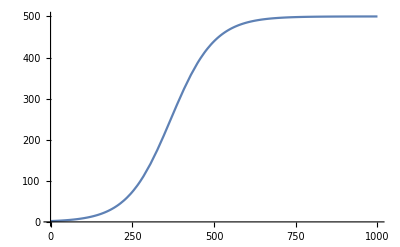

```mathematica
Plot[fLogistic[t,0.015, 500],{t,0,1000}]
```

```mathematica
LogLikelihood[NormalDistribution[0, 10],residual]
```

-37.6544

```mathematica
σ=10
```

10

```mathematica
D[-(1/(2 σ^2))Sum[(y[[i]]-fLogistic[t[[i]],r,κ])^2,{i,1,Length@y,1}],r]/.{r->0.015,κ->500}
```

-4888.46

```mathematica
D[-(1/(2 σ^2))Sum[(y[[i]]-fLogistic[t[[i]],r,κ])^2,{i,1,Length@y,1}],κ]/.{r->0.015,κ->500}
```

0.0683546